## 3.029 Spring 2022 Lecture 14 - 03/16/2022

## Solution Models

We will return to our study of thermodynamic systems, and in particular investigate multicomponent systems

This is often referred to as “chemical thermodynamics” or “solution theory”

In this lecture, we will investigate the ideal and regular solution models

This will prepare us to look at binary phase diagrams after the break

## Partial Molar Quantities

### Formal Definition

Recall from L05-L06 and your thermodynamic courses that the fundamental thermodynamic relation is given by

(in the absence of additional work terms due to magnetization/polarization etc)

which gives the Euler Equality:

whose natural variables are the Entropy, Volume, and mole number of component j

Performing a Legendre transform, we can obtain the Gibbs Free energy as

With differential form:

Partial derivative of the Gibbs differential terms with respect to  are called partial molar quantities

E.g. the first partial derivative of the Gibbs free Energy with pressure at constant temperature and  is given by

Giving the mixed partial derivative of the Gibbs free Energy with pressure and mole number  at constant temperature and

Quick note on (imo confusing) notation

Molar quantities are intensive properties obtained by normalizing an extensive property by the number of moles

They are typically represented with an underbar

E.g. the molar volume of pure Ni would be

Partial molar quantities are intensive properties obtained by taking a partial derivative of an extensive property, wrt to the number of moles of a component

They are typically represented with an overbar

E.g. as we saw above, the partial molar volume is given by

The most common example is the chemical potential, given by

### Partial Molar Volume Example

Let’s consider a solution made of water and ethanol

and take a look at the partial molar volume equation more closely

This is measuring how much the total volume of the solution is changing  when we add more/less of one of the compounds

In general, the volume of a solution is not equal to the sum of the volume of its individual components

E.g. the figure below (data from Moore 1972) shows the partial molar volumes of ethanol and water as a function of ethanol mole fraction

We can see that for nearly all concentrations of ethanol, the partial molar volumes are lower than their pure values.
I.e. mixing water with ethanol results in a contraction of the solution’s volume!

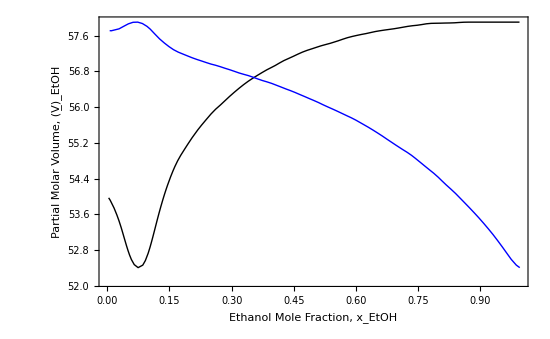

```mathematica
[{,},Joined->True,PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick]},
"SecondaryAxesColor"->Blue,ImageSize->550,LabelStyle->Directive[Black,16],ImagePadding->{{65,50},{50,10}},
FrameLabel->{{"Partial Molar Volume, (V̲)_EtOH",Style["Partial Molar Volume, (V̲)_H20",Blue]},{"Ethanol Mole Fraction, x_EtOH",None}}]
```

In-fact, we can quantify this relative to the volume the solution would have given its components’ concentration and partial molar volumes

This is called the excess volume of mixing and for the water - Ethanol system is given by (data digitized from Wikimedia commons)

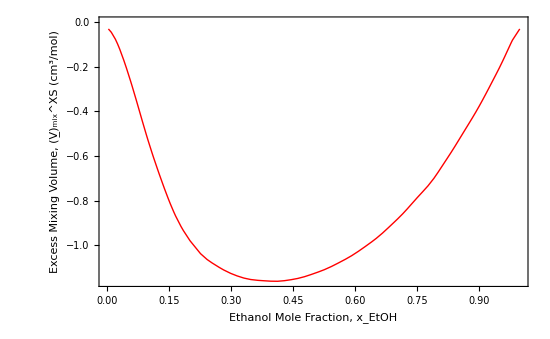

```mathematica
ListLinePlot[,Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,ImagePadding->{{65,50},{50,10}},FrameLabel->{"Ethanol Mole Fraction, x_EtOH","Excess Mixing Volume, (V̲)_mix^XS (cm^3/mol)"},PlotStyle->Directive[Red,Thick]]
```

### Tangent - Intercept Rule

A nice property of partial molar quantities is that they can be read from graphs of the relevant molar quantities as a function of composition

using the tangent-intercept rule

E.g. consider the following molar entropy of a solution function

```mathematica
molarEntropy[x_]=x Log[x]+(1-x)Log[1-x]-x/2
```

-x/2+(1-x) Log[1-x]+x Log[x]

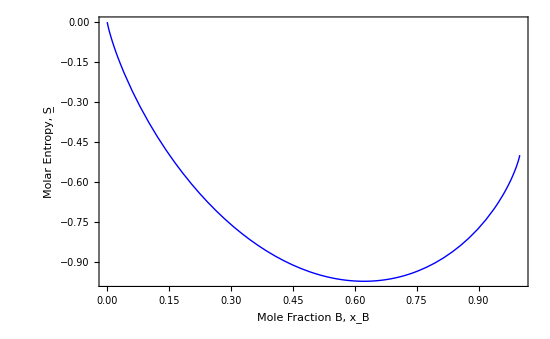

```mathematica
Plot[molarEntropy[x],{x,0,1},Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,ImagePadding->{{65,50},{50,10}},FrameLabel->{"Mole Fraction B, x_B","Molar Entropy, S̲"},PlotStyle->Directive[Blue,Thick]]
```

The partial molar entropy of A as a function of composition,  is given by

```mathematica
partialMolarEntropyA[x_]=molarEntropy[x]-x molarEntropy'[x]
partialMolarEntropyB[x_]=molarEntropy[x]+(1-x) molarEntropy'[x]
```

-x/2+(1-x) Log[1-x]+x Log[x]-x (-1/2-Log[1-x]+Log[x])

-x/2+(1-x) Log[1-x]+x Log[x]+(1-x) (-1/2-Log[1-x]+Log[x])

```mathematica
Manipulate[
Plot[molarEntropy[x],{x,0,1},Epilog->{PointSize[Large],Point[{xB,molarEntropy[xB]}],Dashed,Line[{{0,partialMolarEntropyA[xB]},{1,partialMolarEntropyB[xB]}}]},Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,ImagePadding->{{65,50},{50,10}},PlotRange->{-2,0},FrameLabel->{"Mole Fraction B, x_B","Molar Entropy, S̲"},PlotStyle->Directive[Blue,Thick]],
{{xB,0.4},0+10^-6,1-10^-6},Paneled->False,SaveDefinitions->True]
```

## Solution Models

The concepts of excess molar quantities of mixing, as well as the tangent-intercept rule motivate us to think about the Gibbs free energy of a solution

To do so, we will need to use some models for the intermolecular interactions of the different components

Later in the semester, once we introduce statistical mechanics, we will code-up the solution model we will use below from scratch

For now, we simply show the simulation to explore the physics and understand the materials-science concepts

### Ideal Solution Model

An ideal solution is one in which the atoms do not interact with one another

That is, interchanging two atoms within the solution causes no potential energy change

Consider a binary (A-B) solution on a square grid

with  atoms

The excess molar Gibbs free energy of mixing for the solution is given by

where  is the molar entropy of mixing

At equilibrium, since there is no penalty to interchange the atoms, the two components are randomly mixed

The number of ways we can arrange  atoms of A and  atoms of B in  sites is given using the following argument:

the first A atom can be placed in any of  sites

the second  atom however only has  sites to choose from

since the two atoms are indistinguishable there are  ways to placing these first two atoms

similarly, the first three atoms can be placed  ways

and so on

As such, the number of possible configurations of  A atoms and  B atoms on a square lattice of  sites is given by

```mathematica
Product[(n-i),{i,0,na-1}]/(na!)
```

((1+n-na) Pochhammer[2+n-na,-1+na])/(na!)

We can ask mathematica to expand this out using “simpler” functions

```mathematica
FunctionExpand[Product[(n-i),{i,0,na-1}]/(na!)]
```

Gamma[1+n]/(Gamma[1+n-na] Gamma[1+na])

This might not look much simpler, but notice that the Gamma function is related to the factorial function for integer arguments according to

```mathematica
FunctionExpand[Product[(n-i),{i,0,na-1}]/(na!)]/.Gamma[a_]:>(a-1)!
```

(n!)/((n-na)! na!)

In-fact, we could’ve gotten this by simply asking Mathematica to tell us the number of ways we can “choose” N_A sites from a total of  sites using the Binomial Coefficient

```mathematica
FunctionExpand[Binomial[n,na]]/.Gamma[a_]:>(a-1)!
```

(n!)/((n-na)! na!)

Switching to a mole fraction description for the B atoms

We obtain the degeneracy as

We know the molar entropy of mixing is then given by

To simplify, we make use of Stirling’s approximation

```mathematica
FullSimplify[Asymptotic[Log[n!],n->∞],n>0]
```

-n+n Log[n]+Log[1+12 n]-1/2 Log[(72 n)/π]

```mathematica
stirlingsApproximationRules={
Log[n_!]:>n Log[n]-n,
Log[a_/b_]:>Log[a]-Log[b],
Log[a_*b_]:>Log[a]+Log[b]
};
```

```mathematica
FullSimplify[Log[ExpandAll[(na!)/((na(1-x))!(na x)!)]]//.stirlingsApproximationRules]
```

na (Log[na]-x (Log[na]+Log[x])+(-1+x) Log[na-na x])

We wish to find the limit of this for large numbers, so we set

```mathematica
Limit[FullSimplify[Log[ExpandAll[(na!)/((na(1-x))!(na x)!)]]//.stirlingsApproximationRules],na->∞]
```

DirectedInfinity[(-1+x) Log[1-x]-x Log[x]]

We know entropy is an extensive property, so this correctly approaches infinity

but notice it approaches it with the form

### Regular Solution Model

In a real solution, components do interact with one another giving rise to an excess Enthalpy of mixing

In the regular solution model, this component interactions are assumed to be pairwise

Pair interaction energies :

EAA : the energy associated with an A—A pair

EBB : the energy associated with an B—B pair

EAB : the energy associated with an A—B pair

Site energies:

EA: the energy of a site occupied by A

EB: the energy of a site occupied by B

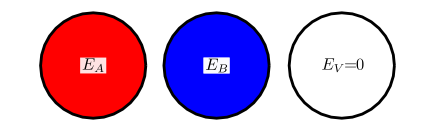

A vacancy has interaction energies and site energy equal to zero

where  is the coordination number of our atoms (first-nearest neighbors)

and

```mathematica
regularSolutionModel[{z_,ω_},RT_][xB_]=(1-xB) xB z ω+RT ((1-xB) Log[1-xB]+xB Log[xB]);
```

```mathematica
Manipulate[
Plot[
regularSolutionModel[{4,ω},temperature][xB],{xB,0,1},PlotStyle->{Red,Thick},Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,FrameLabel->{"Mole Fraction B, x_B","Molar Gibbs Energy, G̲"}],
{ω,-5,5},
{temperature,.001,10},
Delimiter,
{{x,0.4},0+10^-6,1-10^-6},SaveDefinitions->True,Paneled->False
]
```

We can use the same tangent-intercept rule to obtain the chemical potentials

```mathematica
chemicalPotentialA[{z_,ω_},RT_][x_]=regularSolutionModel[{z,ω},RT][x]-x regularSolutionModel[{z,ω},RT]'[x];
chemicalPotentialB[{z_,ω_},RT_][x_]=regularSolutionModel[{z,ω},RT][x]+(1-x) regularSolutionModel[{z,ω},RT]'[x];
```

```mathematica
Manipulate[
Plot[
regularSolutionModel[{4,ω},temperature][xB],{xB,0,1},PlotStyle->{Red,Thick},Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,Epilog->{PointSize[Large],Point[{x,regularSolutionModel[{4,ω},temperature][x]}],Dashed,Line[{{0,chemicalPotentialA[{4,ω},temperature][x]},{1,chemicalPotentialB[{4,ω},temperature][x]}}]},FrameLabel->{"Mole Fraction B, x_B","Molar Gibbs Energy, G̲"}],
{ω,-5,5},
{temperature,.001,10},Delimiter,
{{x,0.4},0+10^-6,1-10^-6},SaveDefinitions->True,Paneled->False
]
```

## Demo!

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"lattice_order_disorder_source.m"}]];
```

```mathematica
orderdisorderSimulation[0,0,0,0][{0.002,0.5,0.5}]
```

4v9iw_shm44FrontEndObject[LinkObject["4v9iw_shm", 3, 1]]44Untitled-1